# Rectangle

### 如何用方程来表达一个矩形

最容易想到的方式

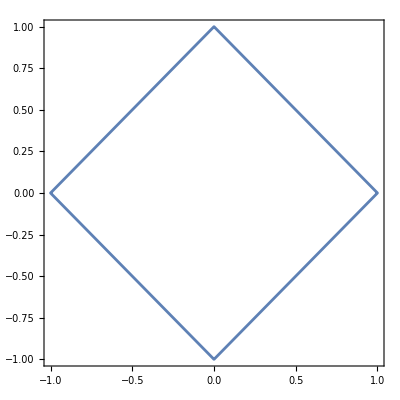

```mathematica
ContourPlot[Abs[x]+Abs[y]==1,{x,-1,1},{y,-1,1}]
```

更强大的形式

```mathematica
Manipulate[ParametricPlot[{Sign[Cos[t]]Abs[Power[Cos[t],n]], Sign[Sin[t]]Abs[Power[Sin[t],n]]},{t,0,2Pi},PlotRange->2],{{n,1},-10,10}]
```

将Abs换个位置

```mathematica
Manipulate[ParametricPlot[{Sign[Cos[t]]Power[Abs[Cos[t]],n], Sign[Sin[t]]Power[Abs[Sin[t]],n]},{t,0,2Pi},PlotRange->4],{{n,1},-10,10}]
```

### 使用参数方程来绘制矩形

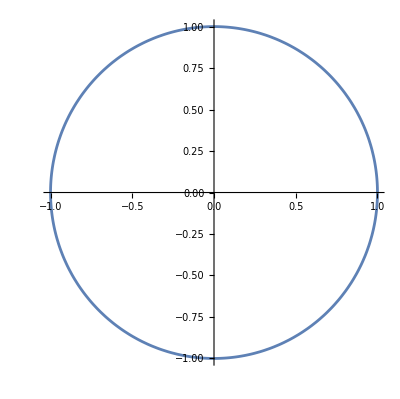

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

使圆的半径随着参数t变化
根据勾股定理，不难算出参数t∈[0，π/2]时

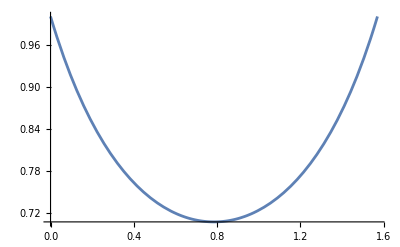

```mathematica
r=1/(Cos[t]+Sin[t]);
Plot[r,{t,0,π/2}]
```

先看看1/4圆修改后的样子

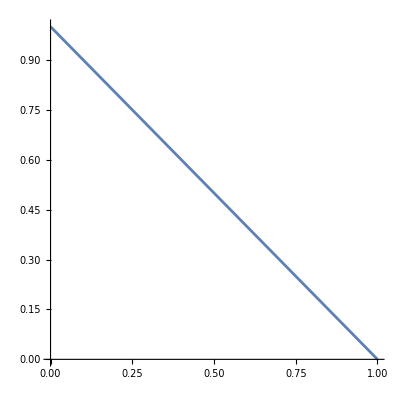

```mathematica
ParametricPlot[r{Cos[t],Sin[t]},{t,0,π/2}]
```

然后，让r在2π的周期内重复4次

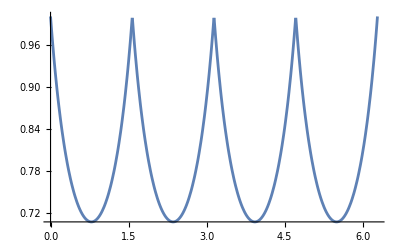

```mathematica
m=Mod[t,π/2];
r=1/(Cos[m]+Sin[m]);
Plot[r,{t,0,2π}]
```

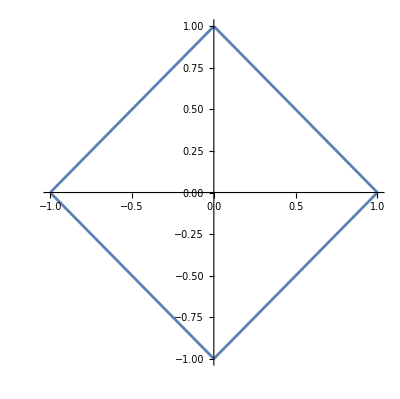

```mathematica
{x,y}=r{Cos[t],Sin[t]};
ParametricPlot[{x,y},{t,0,2Pi}]
```

让它旋转，缩放

```mathematica
Manipulate[ParametricPlot[l{x,y}.RotationMatrix[n],{t,0,2Pi},PlotRange->1],{n,0,2π},{{l,1},0.1,2}]
```

以此类推，正五边形该怎么表达呢？

```mathematica
a0=2π/n;
a1=(π-a0)/2;
x=Tan[t]/(Tan[t]+Tan[a1]);
r=(x Tan[a1])/Sin[t]
(*r=Tan[a1]/(Sin[t]+Cos[t]Tan[a1]);*)
```

(Sec[t] Tan[1/2 (π-(2 π)/n)])/(Tan[1/2 (π-(2 π)/n)]+Tan[t])

```mathematica
m=Mod[t,a0];
r=r/.t->m
```

(Sec[Mod[t,(2 π)/n]] Tan[1/2 (π-(2 π)/n)])/(Tan[1/2 (π-(2 π)/n)]+Tan[Mod[t,(2 π)/n]])

```mathematica
polyR[n_,t_]:=(Sec[Mod[t,(2 π)/n]] Tan[1/2 (π-(2 π)/n)])/(Tan[1/2 (π-(2 π)/n)]+Tan[Mod[t,(2 π)/n]])
Manipulate[Plot[polyR[n,t],{t,0,2π},PlotRange->{0,1}],{n,3,10,1}]
```

```mathematica
Manipulate[ParametricPlot[l polyR[n,t+θ]{Cos[t],Sin[t]},{t,0,2Pi},PlotRange->1],{n,3,10,1},{θ,0,2π},{{l,1},0.1,2}]
```

到这里想到了什么？
极坐标

### 想一想，3D世界里会有怎样效果？